```mathematica
spec=<|MaxTime->10,SampleRate->100,Components->{<|Amplitude->2,Frequency->20,TStart->1,TEnd->10|>,<|Amplitude->3,Frequency->32,TStart->3,TEnd->6|>,<|Amplitude->1,Frequency->6,TStart->2,TEnd->5|>}|>;


data=Table[{t,Total@Map[If[#[TStart]<=t<=#[TEnd],1,0]*#[Amplitude]*Sin[2 Pi t #[Frequency]]&,spec[Components]]},{t,0,spec[MaxTime],1/spec[SampleRate]}];


extractSignal[data_,tStart_,tEnd_]:=Select[data,tStart<=#[[1]]<=tEnd&];


cutData=extractSignal[data,2.5,4.5];
```

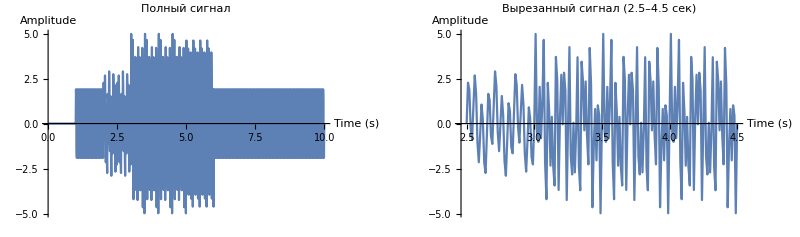

-Graphics-

```mathematica
p1=ListLinePlot[data,PlotRange->All,AxesLabel->{"Time (s)","Amplitude"},PlotLabel->"Полный сигнал"];


p2=ListLinePlot[cutData,PlotRange->All,AxesLabel->{"Time (s)","Amplitude"},PlotLabel->"Вырезанный сигнал (2.5–4.5 сек)"];


GraphicsRow[{p1,p2}]
```